```mathematica
α=7.297352533 10^-3;
H[x_,y_,β_]:=(α*β)/(2*π)*(1/(√(x*(1-x)))*ArcTan[√(x/(1-x))]-1+π(λ[y,β] x)/(1-x-λ[y,β]^2)) Exp[-(2y)/β];
H0[x_,y_,β_]:= α*β*(1/(4 √(1-x))+1/2 λ[y,β]/(1-x-λ[y,β]^2)) Exp[-(2y)/β];
dH[x_,y_,β_]:=((x+(2 *x -1))/(2*x^2*(1-x)) √(x/(1-x))ArcTan[ √(x/(1-x))]+(π(1-λ[y,β])^2 λ[y,β])/((1-λ[y,β]^2-x)^2))Exp[-(2y)/β];
u1[y_,β_]:=(2 β^2)/(α^2 y^2)*Exp[ExpIntegralEi[-(2y)/β]];
λ[y_,β_]:= α/2 (Log[4.5 u1[y,β]]-2.44 Log[Log[0.15 u1[y,β]]]);
```

```mathematica
LDis22:={0,0.17152373120951317,0.25425675253552055,0.3343215848791908,0.41114617023692224,0.48406463187565596,0.552333359727247,0.6151809287823247,0.6718999917624312,0.7219727197088988,0.7651932482413231,0.8017320108523674,0.8321049531672834,0.8570611804631143,0.8774427921507677,0.8940691145057108,0.9076678989329952,0.9188490739262715,0.9281058068656158,0.9358286878921254,0.9423238591914328,0.9478304174957317,0.9525352652838618,0.9565850536620782,0.9600954860541003,0.9631584465657028,0.9658474201956867,0.9682216056748036,0.9703290406835073,0.9722089853155622,0.9738937486980306,0.975410097452239,0.9767803482267107,0.978023220934195,0.979154509456122,0.9801876123423393,0.9811339554455123,0.9820033306153388,0.982804168780894,0.9835437614287982,0.9842284412476582,0.9848637302676115,0.9854544619961811,0.98600488257092,0.9865187350136578,0.9869993296583117,0.9874496033230019,0.9878721692216844,0.9882693592367303,0.9886432598603934,0.9889957428669844,0.9893284915815347,0.989643023454172,0.9899407095234488,0.9902227912503302,0.990490395122196,0.9907445453592194,0.9909861750007114,0.9912161356041207,0.9914352057523746,0.9916440985346897,0.9918434681242042,0.9920339156856426,0.9922159943720358,0.992390214063252,0.9925570453589425,0.992716923221621,0.9928702502156607,0.9930173994044347,0.9931587169540738,0.9932945244496337,0.9934251210082262,0.993550785159603,0.9936717765523335,0.9937883374941954,0.9939006943464167,0.9940090587875093,0.9941136289605335,0.9942145905160449,0.9943121175614426,0.9944063735262976,0.9944975119521621,0.9945856772141984,0.9946710051815255,0.9947536238220548,0.9948336537571846,0.9949112087710711,0.9949863962787134,0.9950593177566438,0.9951300691396254,0.9951987411864143,0.9952654198173327,0.995330186426132,0.9953931181683746,0.995454288223814,0.9955137660655716,0.9955716176478797,0.9956279056567562,0.9956826896921211,0.9957360264527614,0.9957879699077595,0.9958385714555362,0.9958878800724461,0.9959359424507371,0.9959828031277471,0.9960285046063768,0.9960730874677051,0.9961165904763043,0.9961590506787965,0.9962005034961421,0.9962409828101192,0.9962805210444069,0.9963191492406592,0.9963568971344409,0.9963937932075069,0.9964298647700149,0.9964651380086401,0.9964996380449235,0.9965333889878499,0.996566413983385,0.9965987352611662,0.9966303741785454,0.9966613512621448,0.9966916862470916,0.9967213981140799,0.9967505051243969,0.9967790248530406,0.9968069742200488,0.9968343695201513,0.9968612264508449,0.9968875601389906,0.9969133851660198,0.996938715591834,0.9969635649774747,0.9969879464066373,0.9970118725060955,0.9970353554650981,0.9970584070538022,0.9970810386405617,0.9971032612094142,0.9971250853752144,0.9971465213979053,0.9971675791987441,0.9971882683727897,0.99720859820213,0.9972285776683789,0.9972482154641482,0.9972675200058919,0.9972864994415962,0.9973051616641467,0.9973235143189406,0.9973415648167724,0.9973593203365404,0.9973767878397857,0.9973939740761293,0.9974108855915175,0.9974275287356663,0.9974439096693706,0.997460034371206,0.9974759086441616,0.997491538121906,0.997506928274497,0.9975220844156389,0.9975370117053461,0.997551715157913,0.9975661996458318,0.9975804699048108,0.9975945305385664,0.9976083860228585,0.9976220407106582,0.9976354988355094,0.9976487645158199,0.9976618417586504,0.9976747344633775,0.9976874464252203,0.997699981338692,0.9977123428005634,0.9977245343135691,0.9977365592889011,0.9977484210493357,0.9977601228320055,0.9977716677910871,0.9977830590003921,0.9977942994558654,0.9978053920779899,0.9978163397141052,0.997827145140642,0.9978378110652762,0.9978483401290055,0.9978587349081562,0.9978689979163071,0.9978791316061633,0.9978891383713495,0.9978990205481492,0.9979087804171791,0.9979184202050109,0.9979279420857302,0.9979373481822499,0.9979466405687486,0.9979558212701808,0.9979648922654378,0.9979738554878188,0.9979827128266259,0.9979914661280028,0.9980001171964541,0.9980086677960391,0.9980171196510784,0.9980254744477488,0.9980337338351445,0.9980418994246728,0.998049972794393,0.998057955486625,0.99806584901061,0.9980736548428184,0.9980813744281136,0.9980890091804139,0.9980965604835355,0.9981040296919717,0.9981114181316454,0.9981187271006337,0.9981259578705121,0.9981331116851351,0.9981401897636528,0.9981471932998328,0.9981541234629805,0.9981609813985528,0.9981677682287519,0.998181132949026,0.9981877129723463,0.9981942261578609,0.9982006735198293,0.998207056052475,0.9982133747304655,0.9982196305093775,0.9982258243266828,0.9982319571004802,0.998238029732118,0.998244043105332,0.9982499980869401,0.9982558955272381,0.9982617362603856,0.9982675211047701,0.9982732508634107,0.9982789263242575,0.9982845482605718,0.9982901174312532,0.9982956345811663,0.9983065157298695,0.9983118811510325,0.9983171973967672,0.998322465146365,0.9983276850668675,0.9983328578133369,0.9983379840291191,0.9983430643461012,0.9983480993849614,0.998353089755412,0.998358036056438,0.9983629388765274,0.9983677987938971,0.9983726163767127,0.9983773921833029,0.9983821267623672,0.9983868206531812,0.9983914743857937,0.998396088481221,0.9984006634516349,0.9984051998005483,0.998409698022993,0.9984141586056957,0.9984185820272493,0.9984229687582791,0.9984273192616057,0.9984316339924034,0.9984359133983561,0.9984401579198076,0.9984443679900472,0.9984485440347878,0.9984526864735755,0.9984567957187552,0.9984608721761182,0.9984649162449071,0.9984689283181165,0.998472908782327,0.998480776399931,0.9984846642964872,0.9984885220705835,0.9984923500794031,0.9984961486745564,0.99849991820219,0.9985036590033024,0.9985073714132215,0.9985110557624595,0.9985147123763849,0.9985183415754096,0.9985219436750822,0.9985255189861776,0.9985290678147868,0.9985325904624034,0.9985360872260093,0.998539558398158,0.9985430042670576,0.9985464251166538,0.9985498212267147,0.9985531928725645,0.998556540326208,0.9985598638550994,0.9985631637229606,0.9985664401896865,0.9985696935114137,0.9985729239405869,0.9985761317260241,0.9985793171129802,0.9985824803432077,0.9985856216550139,0.9985887412833094,0.99859183945998,0.9985949164130432,0.998597972367787,0.9986010075462188,0.998604022167251,0.9986070164467534,0.9986099905976102,0.9986129448297582,0.9986158793502515,0.9986187943633033,0.9986216900703335,0.9986245666700178,0.9986274243583324,0.9986302633286002,0.998633083771534,0.9986358858752807,0.9986386698254637,0.9986414358052241,0.9986441839952626,0.9986469145738779,0.9986496277170079,0.9986523235982675,0.9986550023889855,0.9986576642582434,0.9986603093729102,0.9986629378976789,0.9986655499951015,0.9986681458256229,0.9986707255476147,0.9986732893174085,0.9986758372893284,0.9986783696157218,0.9986808864469917,0.9986908017625309,0.9986932433082744,0.9986956702221477,0.9986980826417667,0.9987004807030321,0.9987028645401527,0.9987052342856866,0.9987075900705361,0.9987099320240035,0.9987122602737998,0.9987145749460722,0.9987168761654277,0.9987191640549563,0.9987214387362536,0.9987237003294435,0.9987259489532,0.9987281847247689,0.998730407759989,0.998732618173313,0.998734816077828,0.9987370015852755,0.9987391748060709,0.9987413358493239,0.9987434848228566,0.9987456218332226,0.9987477469856441,0.9987498603843753,0.9987519621321691,0.998754052330687,0.9987561310804116,0.9987581984806625,0.9987602546296137,0.9987622996243094,0.9987643335606803,0.9987663565335594,0.9987683686366975,0.9987703699627787,0.9987723606034351,0.9987743406492615,0.9987763101898304,0.9987782693137058,0.9987802181084579,0.9987821566606757,0.9987840850559818,0.9987860033790453,0.9987879117135949,0.9987898101424316,0.998791698747442,0.9987935776096103,0.9987954468090308,0.99879730642492,0.9987991565356285,0.9988009972186526,0.9988028285506461,0.998804650607361,0.998806463463969,0.9988082671945528,0.998810061872511,0.9988118475704534,0.9988136243602113,0.9988153923128484,0.9988171514986717,0.9988189019872401,0.9988206438473763,0.998822377147175,0.9988241019540132,0.9988258183345593,0.9988275263547827,0.9988292260799625,0.9988309175747189,0.9988326009029141,0.9988342761278668,0.9988359433121707,0.9988376025177836,0.9988392538060138,0.9988408972375908,0.9988425328725454,0.9988441607703448,0.9988457809898277,0.998847393589271,0.9988489986263046,0.9988505961580111,0.9988521862408793,0.9988537689308665,0.9988553442833076,0.9988569123530237,0.9988584731942768,0.9988600268607892,0.9988615734057535,0.9988631128817974,0.9988646453410902,0.998866170835241,0.9988676894153615,0.9988692011320602,0.9988707060354471,0.9988722041751315,0.9988736956003081,0.9988751803595707,0.9988766585011277,0.9988781300726977,0.9988795951215184,0.9988810536944485,0.9988825058377752,0.9988896717021405,0.9988910862167888,0.9988924946141361,0.9988938969371157,0.9988952932282564,0.9988966835296862,0.9988980678831384,0.9988994463299553,0.9989008189110932,0.9989021856671264,0.9989035466382523,0.9989049018642949,0.9989062513847102,0.9989075952385893,0.9989089334646634,0.9989102661013072,0.998911593186544,0.9989129147580489,0.9989142308531526,0.9989155415088462,0.9989168467617842,0.9989181466482888,0.9989194412043534,0.9989207304656464,0.9989220144675152,0.9989232932449885,0.9989245668327816,0.9989258352652991,0.9989270985766381,0.9989283568005917,0.9989296099706526,0.9989308581200169,0.9989321012815863,0.9989333394879719,0.9989345727714977,0.9989358011642031,0.9989370246978465,0.9989382434039082,0.9989394573135936,0.9989406664578354,0.998941870867298,0.9989430705723793,0.9989442656032136,0.9989454559896751,0.9989466417613801,0.9989478229476901,0.9989489995777145,0.9989501716803129,0.9989513392840985,0.9989525024174399,0.9989536611084645,0.9989548153850604,0.9989559652748793,0.998957110805339,0.9989582520036254,0.998959388896696,0.9989605215112808,0.9989616498738861,0.9989627740107959,0.9989638939480748,0.9989650097115681,0.9989661213269106,0.9989672288195203,0.9989683322146052,0.9989694315371657,0.9989705268119952,0.9989716180636827,0.9989727053166159,0.9989737885949814,0.9989748679227687,0.9989759433237749,0.9989770148216008,0.9989780824396478,0.9989791462011333,0.9989802061290863,0.9989812622463502,0.9989823145755835,0.9989833631392621,0.9989844079596825,0.9989854490589589,0.9989864864590321,0.9989875201816663,0.9989885502484518,0.9989895766808075,0.9989905994999819,0.9989916187270553,0.9989926343829411,0.9989936464883873,0.9989946550639792,0.9989956601301394,0.9989966617071306,0.9989976598150567,0.9989986544738647,0.9989996457033454,0.9990006335231363,0.9990016179527211,0.9990025990114176,0.9990035767184496,0.9990045510928238,0.999005522153431,0.9990064899190153,0.9990074544081766,0.9990084156393718,0.9990093736309164,0.9990103284009859,0.9990112799676173,0.9990122283487104,0.999013173562029,0.9990141156252021,0.9990150545557257,0.9990159903709473,0.9990169230881413,0.9990178527243802,0.9990187792966417,0.9990197028217755,0.9990206233165027,0.9990215407974207,0.9990224552810032,0.9990233667836006,0.9990242753214423,0.9990251809106372,0.9990260835671754,0.9990269833069167,0.9990278801456491,0.9990287740989836,0.9990296651824497,0.9990305534114595,0.9990314388013111,0.9990323213671906,0.9990332011241737,0.9990340780872132,0.9990349522712006,0.9990358236908558,0.999036692360836,0.9990375582956674,0.9990384215097879,0.999039282017526,0.9990401398331077,0.9990409949706567,0.9990418474441956,0.9990426972676238,0.9990435444548313,0.9990443890194844,0.9990452309752226,0.9990460703355805,0.9990469071139936,0.9990477413238021,0.9990485729782457,0.9990494020904959,0.9990502286735975,0.9990510527405225,0.9990518743041501,0.999057556220288,0.9990583582105096,0.9990591578093976,0.9990599550289391,0.999060749881074,0.9990615423776504,0.9990623325304212,0.9990631203511169,0.9990639058512826,0.9990646890425076,0.9990654699362161,0.99906624854377,0.9990670248764775,0.9990677989455521,0.9990685707621336,0.9990693403372926,0.9990701076820268,0.9990708728072576,0.9990716357238129,0.9990723964425198,0.9990731549740223,0.9990739113289827,0.9990746655179485,0.9990754175514138,0.9990761674398058,0.999076915193456,0.9990776608226678,0.9990784043376466,0.99907914574855,0.9990798850654494,0.9990806222983626,0.9990813574572411,0.9990820905519672,0.999082821592361,0.999083550588179,0.9990842775491098,0.9990850024847908,0.9990857254047839,0.9990864463185882,0.9990871652356549,0.9990878821653582,0.999088597117037,0.9990893100999357,0.999090021123263,0.9990907301961619,0.9990914373277192,0.9990921425269682,0.9990928458028446,0.9990935471642991,0.9990942466201729,0.999094944179265,0.9990956398503189,0.9990963336420221,0.999097025563007,0.9990977156218503,0.999098403827089,0.9990990901871785,0.9990997747105425,0.9991004574055454,0.9991011382805003,0.9991018173436675,0.9991024946032566,0.9991031700674252,0.9991038437442806,0.99910451564188,0.9991051857682302,0.9991058541312886,0.9991065207389633,0.9991071855991139,0.9991078487195508,0.9991085101080365,0.999109169772285,0.9991098277199889,0.9991104839587336,0.9991111384961083,0.9991117913396416,0.999112442496816,0.9991130919750686,0.9991137397817914,0.9991143859243317,0.9991150304099922,0.9991156732460315,0.9991163144396641,0.9991169539980529,0.9991175919283523,0.9991182282376213,0.9991188629329121,0.9991194960212249,0.9991201275095188,0.9991207574047115,0.9991213857136788,0.999122012443256,0.9991226376002379,0.9991232611913782,0.9991238832233913,0.9991245037029579,0.9991257400312323,0.9991263558930965,0.9991269702288168,0.9991275830448737,0.9991281943477086,0.9991288041437255,0.9991294124393033,0.9991300192407584,0.9991306245543894,0.9991312283864533,0.9991318307431709,0.9991324316307266,0.9991330310552693,0.9991336290229111,0.999134225539728,0.9991348206117785,0.9991354142450517,0.9991360064455284,0.999136597219148,0.9991371865718164,0.9991377745094049,0.999138361037752,0.9991389461626624,0.9991395298899082,0.9991401122252281,0.9991406931743285,0.9991412727428838,0.9991418509365352,0.9991424277608921,0.9991430032215453,0.9991435773240247,0.9991441500738529};
```

```mathematica
LDis33 :={0.9991447214765147,0.9991452915374649,0.9991458602621266,0.9991464276558842,0.9991469937241291,0.9991475584721645,0.9991481219053078,0.999148684028829,0.999149244847974,0.9991498043679562,0.9991503625939713,0.9991509195311684,0.9991514751846803,0.9991520295596087,0.9991525826610271,0.9991531344939835,0.9991536850634868,0.999154234374537,0.9991547824320913,0.9991553292410943,0.9991558748064459,0.9991564191330214,0.9991569622257074,0.9991575040893023,0.9991580447286096,0.999158584148433,0.9991591223535048,0.9991596593485493,0.9991601951382708,0.999160729727344,0.9991612631204188,0.9991617953221145,0.9991623263370469,0.9991628561697757,0.999163384824857,0.9991639123068172,0.9991644386201591,0.999164963769361,0.9991654877588775,0.9991660105931396,0.9991665322765549,0.999167052813502,0.9991675722083563,0.9991680904654451,0.9991686075890844,0.9991691235835674,0.9991696384531639,0.9991701522021212,0.9991706648346649,0.9991711763549976,0.9991716867673006,0.9991721960757332,0.9991727042844325,0.9991732113975126,0.9991737174190746,0.9991742223531855,0.9991747262038994,0.9991752289752475,0.9991757306712465,0.9991762312958673,0.9991767308530971,0.9991772293468792,0.9991777267811415,0.9991782231597925,0.9991787184867204,0.9991792127657928,0.9991797060008584,0.9991801981957461,0.999180689354265,0.9991811794802049,0.9991816685773364,0.999182156649411,0.9991826437001576,0.9991831297332987,0.9991836147525217,0.9991840987615036,0.9991845817639023,0.999185063763357,0.9991855447634933,0.9991860247678991,0.9991865037801732,0.9991869818038767,0.9991874588425619,0.9991879348997523,0.9991884099789685,0.9991888840837023,0.9991893572174335,0.9991898293836226,0.9991903005857133,0.9991907708271333,0.9991912401112903,0.9991917084415795,0.9991921758213759,0.9991926422540394,0.9991931077429104,0.9991935722913233,0.9991940359025804,0.999194498579978,0.9991949603267941,0.9991954211462906,0.999195881041713,0.9991963400162915,0.9991967980732405,0.9991972552157581,0.9991977114470277,0.9991981667702169,0.9991986211884778,0.9991990747049473,0.9991995273227471,0.9991999790449841,0.9992004298747501,0.9992008798151228,0.9992013288691625,0.9992017770399171,0.9992022243304243,0.9992026707436876,0.9992031162827234,0.9992035609505217,0.9992040047500519,0.9992044476842765,0.9992048897561429,0.9992053309685832,0.9992057713245166,0.9992062108268479,0.9992066494784686,0.9992070872822559,0.9992075242410743,0.9992079603577736,0.9992083956351913,0.9992088300761507,0.9992092636834622,0.9992096964599232,0.9992101284083172,0.9992105595314158,0.9992109898319766,0.9992114193127448,0.9992118479764529,0.9992122758258202,0.9992127028635539,0.9992131290923482,0.9992135545148849,0.9992139791338315,0.9992144029518506,0.9992148259715821,0.9992152481956595,0.9992156696267017,0.9992160902673223,0.9992165101201124,0.9992169291876579,0.9992173474725313,0.9992177649772924,0.999218181704494,0.9992185976566692,0.9992190128363453,0.9992194272460363,0.999219840888245,0.9992202537654628,0.9992206658801697,0.9992210772348344,0.9992214878319146,0.9992218976738565,0.9992223067630958,0.9992227151020576,0.9992231226931542,0.9992235295387881,0.9992239356413515,0.9992243410032252,0.9992247456267795,0.9992251495143742,0.9992255526683584,0.9992259550910685,0.9992263567848385,0.9992267577519812,0.9992271579948048,0.9992275575156067,0.999227956316674,0.9992283544002868,0.999228751768702,0.9992291484241854,0.9992295443689811,0.9992299396053256,0.9992303341354444,0.9992307279615581,0.9992311210858706,0.99923151351058,0.9992319052378749,0.9992322962699318,0.9992326866089238,0.9992338534890338,0.9992342410772515,0.9992346279831028,0.9992350142087024,0.9992353997561518,0.9992357846275458,0.999236168824966,0.9992365523504989,0.9992369352062014,0.9992373173941349,0.9992376989163491,0.999238079774884,0.9992384599717716,0.9992388395090348,0.999239218388688,0.9992395966127364,0.9992399741831821,0.999240351101999,0.9992407273711813,0.9992411029926951,0.9992414779685085,0.9992418523005697,0.9992422259908276,0.9992425990412203,0.9992429714536777,0.9992433432301217,0.9992437143724657,0.9992440848826147,0.9992444547624653,0.999244824013913,0.999245192638832,0.9992455606390985,0.9992459280165781,0.9992462947731284,0.9992466609105997,0.9992470264308335,0.9992473913356629,0.9992477556269237,0.9992481193064245,0.999248482375981,0.9992488448373968,0.999249206692469,0.9992495679429864,0.9992499285907309,0.9992502886374767,0.9992506480849906,0.999251006935032,0.9992513651893544,0.9992517228497018,0.9992520799178122,0.9992524363954167,0.9992527922842387,0.9992531475859948,0.9992535023023945,0.9992538564351403,0.9992542099859276,0.999254562956445,0.9992549153483719,0.9992552671633892,0.9992556184031598,0.9992559690693457,0.9992563191636015,0.9992566686875749,0.999257017642907,0.9992573660312322,0.9992577138541765,0.9992580611133653,0.9992584078104092,0.9992587539469173,0.9992590995244913,0.9992594445447264,0.9992597890092083,0.9992601329195275,0.9992604762772521,0.999260819083954,0.9992611613411967,0.9992615030505368,0.9992618442135264,0.9992621848317088,0.999262524906623,0.9992628644398012,0.99926320343277,0.9992635418870492,0.9992638798041531,0.9992642171855897,0.9992645540328584,0.999264890347464,0.9992652261308883,0.9992655613846181,0.999999581290337,0.9999995831346787,0.9992665639823997,0.9992668971320786,0.9992672297594011,0.9992675618658128,0.9992678934527585,0.9992682245216767,0.9992685550740004,0.9992688851111575,0.9992692146345666,0.9992695436456467,0.9992698721458059,0.9992702001364528,0.9992705276189849,0.9992708545947947,0.9992711810652741,0.9992715070318066,0.9992718324957629,0.9992721574585236,0.9992724819214541,0.9992728058859156,0.9992731293532653,0.9992734523248548,0.9992737748020304,0.9992740967861335,0.9992744182785002,0.9992747392804612,0.9992750597933425,0.9992753798184651,0.9992756993571447,0.9992760184106919,0.9992763369804105,0.9992766550676071,0.9992769726735719,0.9992772897995974,0.99927760644697,0.9992779226169705,0.9992782383108751,0.9992785535299554,0.9992788682754782,0.9992791825487045,0.9992794963508913,0.9992798096832951,0.9992801225471581,0.9992804349437253,0.9992807468742348,0.9992810583399206,0.9992813693420114,0.9992816798817317,0.9992819899603012,0.9992822995789353,0.9992826087388447,0.9992829174412353,0.9992832256873097,0.9992835334782625,0.999283840815292,0.9992841476995815,0.9992844541323166,0.9992847601146767,0.9992850656478371,0.9992853707329689,0.9992856753712381,0.9992859795638074,0.9992862833118348,0.9992865866164701,0.9992868894788735,0.9992871919001795,0.9992874938815326,0.9992877954240699,0.9992880965289244,0.999288397197223,0.9992886974300915,0.9992889972286499,0.999289296594014,0.9992895955272971,0.9992898940296058,0.9992901921020448,0.9992904897457141,0.9992907869617094,0.9992910837511223,0.9992913801150437,0.9992916760545546,0.9992919715707362,0.999292266664665,0.9992925613374134,0.99929285559005,0.9992931494236394,0.9992934428392427,0.9992937358379169,0.9992940284207154,0.9992943205886872,0.9992946123428766,0.9992949036843326,0.9992951946140857,0.9992954851331731,0.9992957752426258,0.9992960649434691,0.999296354236731,0.9992966431234293,0.9992969316045791,0.9992972196811936,0.999297507354282,0.9992977946248501,0.9999997335495537,0.9999997346874779,0.9992986540314305,0.9992989397019029,0.9992992249748279,0.9992995098511909,0.9992997943319731,0.9993000784181493,0.9993003621107022,0.9993006454105936,0.9993009283187938,0.9993012108362666,0.999301492963971,0.9993017747028683,0.9993020560539085,0.9993023370180429,0.9993026175962187,0.9993028977893801,0.9993031775984673,0.9993034570244178,0.9993037360681654,0.9993040147306406,0.9993042930127723,0.9993045709154835,0.9993048484396959,0.9993051255863272,0.9993054023562928,0.9993056787505039,0.9993059547698665,0.9993062304152932,0.99930650568768,0.9993067805879273,0.9993070551169317,0.9993073292755836,0.9993076030647808,0.9993078764854024,0.9993081495383349,0.9993084222244593,0.9993086945446531,0.9993089664997916,0.9993092380907462,0.9993095093183864,0.9993097801835785,0.999310050687184,0.9993103208300638,0.9993105906130778,0.9993108600370763,0.9993111291029122,0.9993113978114343,0.999311666163488,0.9993119341599161,0.999312201801559,0.9993124690892535,0.9993127360238326,0.9993130026061321,0.9993132688369765,0.9993135347171933,0.9993138002476056,0.9993140654290339,0.9993143302622958,0.9993145947482062,0.9993148588875769,0.9999997951994208,0.999999796059582,0.999999796915908,0.9999997977684177,0.999316174414591,0.999316436491635,0.9993166982277508,0.9993169596237261,0.9993172206803572,0.9993174813984238,0.9993177417787097,0.9993180018219955,0.9993182615290593,0.9993185209006769,0.9993187799376206,0.9993190386406614,0.9993192970105665,0.9993195550480981,0.9993198127540286,0.9993200701291087,0.9993203271740994,0.9993205838897558,0.9993208402768308,0.9993210963360748,0.9993213520682356,0.999321607474059,0.9993218625542877,0.9993221173096655,0.9993223717409219,0.9993226258488009,0.9993228796340339,0.9993231330973507,0.9993233862394826,0.9993236390611535,0.9993238915630883,0.9993241437460078,0.9993243956106336,0.9993246471576807,0.9993248983878643,0.999325149301897,0.9993253999004889,0.9993256501843475,0.9993259001541787,0.9993261498106857,0.9993263991545714,0.9993266481865327,0.9993268969072666,0.9993271453174674,0.9993273934178272,0.9993276412090362,0.9993278886917821,0.9993281358667505,0.9993283827346249,0.9999998359055923,0.9999998365856386,0.9999998372627007,0.9993293671487751,0.9993296124913552,0.9993298575308964,0.9993301022680674,0.9993303467035344,0.9993305908379616,0.999330834672011,0.9993310782063428,0.999331321441614,0.9993315643784839,0.9993318070176025,0.9993320493596232,0.9993322914051953,0.9993325331549671,0.9993327746095837,0.9993330157696894,0.9993332566359253,0.9993334972089315,0.9993337374893454,0.9993339774778031,0.9993342171749363,0.9993344565813812,0.9993346956977642,0.9993349345247136,0.9993351730628555,0.9993354113128139,0.9993356492752109,0.9993358869506666,0.9993361243397991,0.9993363614432248,0.9993365982615583,0.9993368347954115,0.9993370710453956,0.9993373070121193,0.9993375426961894,0.9993377780982107,0.9993380132187866,0.9993382480585182,0.9993384826180051,0.999338716897845,0.9993389508986338,0.999339184620964,0.9993394180654314,0.9993396512326232,0.999339884123129,0.9993401167375354,0.9993403490764277,0.9993405811403918,0.9993408129300003,0.9993410444458424,0.9993412756884924,0.9993415066585268,0.99934173735652,0.9993419677830447,0.9993421979386704,0.9993424278239713,0.9993426574395098,0.9993428867858538,0.9993431158635684,0.9993433446732123,0.9993435732153504,0.9993438014905381,0.9993440294993368,0.9993442572423025,0.9993444847199862,0.999344711932941,0.999344938881718,0.9993451655668666,0.999345391988934,0.9993456181484647,0.9993458440460077,0.9993460696821009,0.9993462950572868,0.999346520172105,0.9993467450270918,0.9993469696227874,0.9993471939597229,0.9993474180384323,0.999347641859447,0.9993478654232971,0.999348088730509,0.9993483117816153,0.9993485345771356,0.9993487571175952,0.9993489794035165,0.99934920143542,0.9993494232138248,0.9993496447392487,0.9993498660122077,0.999350087033216,0.9993503078027871,0.999350528321434,0.9993507485896628,0.9993509686079844,0.9993511883769062,0.9993514078969336,0.9993516271685706,0.99935184619232,0.9993520649686829,0.9993522834981591,0.9993525017812468,0.9993527198184421,0.9993529376102428,0.9993531551571406,0.999353372459629,0.9993535895181965,0.9993538063333396,0.9993540229055397,0.9993542392352873,0.9993544553230662,0.9993546711693615,0.9993548867746559,0.9993551021394295,0.9993553172641637,0.9993555321493366,0.9993557467954253,0.9993559612029057,0.9993561753722521,0.9993563893039384,0.9993566029984354,0.9993568164562112,0.9993570296777432,0.9993572426634908,0.9993574554139231,0.9999999024126153,0.9999999028054511,0.9999999031966236,0.9993583040717822,0.9993585156525882,0.9993587270008505,0.9993589381170255,0.999359149001569,0.999359359654936,0.9993595700775799,0.9993597802699554,0.9993599902325081,0.99936019996569,0.9993604094699493,0.9993606187457332,0.9993608277934878,0.9993610366136574,0.9993612452066853,0.9993614535730136,0.9993616617130833,0.9993618696273336,0.999362077316203,0.9993622847801285,0.9993624920195462,0.9993626990348906,0.9993629058265951,0.9993631123950911,0.9993633187408127,0.999363524864187,0.9993637307656433,0.9993639364456075,0.999364141904511,0.9993643471427729,0.9993645521608213,0.9993647569590771,0.9993649615379621,0.9993651658978977,0.9993653700393007,0.9993655739625917,0.9993657776681869,0.9993659811565024,0.9993661844279524,0.9993663874829506,0.9993665903219097,0.9993667929452419,0.9993669953533537,0.9993671975466579,0.9993673995255614,0.9993676012904705,0.9993678028417913,0.9993680041799281,0.9993682053052836,0.9993684062182633,0.9993686069192651,0.9993688074086904,0.9993690076869383,0.9993692077544066,0.9993694076114918,0.9993696072585919,0.9993698066960998,0.999370005924409,0.9993702049439132,0.9993704037550026,0.9993706023580703,0.9993708007535033,0.9993709989416891,0.9993711969230205,0.9993713946978786,0.9993715922666503,0.999371789629719,0.9993719867874705,0.9993721837402846,0.9993723804885412,0.9993725770326264,0.9993727733729135,0.9993729695097843,0.9993731654436107,0.9993733611747739,0.9993735567036476,0.9993737520306056,0.9993739471560211,0.9993741420802662,0.9993743368037121,0.9993745313267285,0.9993747256496857,0.9993749197729507,0.9993751136968902,0.9993753074218723,0.9993755009482613,0.9993756942764214,0.999375887406716,0.9993760803395074,0.9993762730751571,0.9993764656140256,0.9993766579564722,0.9993768501028557,0.9993770420535335,0.9993772338088623,0.999377425369198,0.9993776167348953,0.999377807906308,0.9993779988837896,0.9993781896676912,0.9993783802583642,0.9993785706561591,0.9993787608614249,0.9993789508745099,0.9993791406957617,0.9993793303255268,0.9993795197641508,0.9993797090119787,0.9993798980693538,0.9993800869366194,0.9993802756141201,0.9993804641021895,0.9993806524011749,0.9993808405114138,0.9993810284332442,0.999381216167005,0.9993814037130315,0.9993815910716599,0.9993817782432259,0.9993819652280631,0.999382152026505,0.9993823386388867,0.9993825250655312};
```

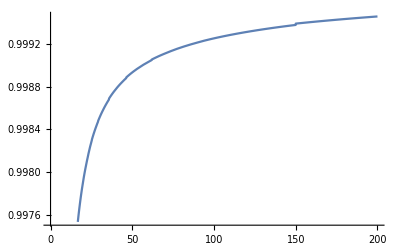

```mathematica
Pl21=ListInterpolation[Re[LDis22],{{0,75}}];
Pl23=ListInterpolation[Re[LDis33],{{75,150}}];
Fd[y_]:=Which[y<75,Pl21[y],75≤y≤150,Pl23[y],y>75,1-λ[y,150]^2];
Plot[Fd[y],{y,0,200}]
```

```mathematica
LDis5=Table[x/.FindRoot[x-y+H[x,y,150],{x,0.9999,0.99999999},MaxIterations->1000],{y,0.0000000001,100,0.1}];
```

```mathematica
LDis5
```

{0.997148,0.999546,0.99959,0.999616,0.999634,0.999649,0.999661,0.999671,0.999681,0.999689,0.999696,0.999703,0.999709,0.999715,0.999721,0.999726,0.999731,0.999736,0.999741,0.999745,0.999749,0.999753,0.999757,0.999761,0.999764,0.999768,0.999771,0.999774,0.999778,0.999781,0.999784,0.999787,0.999789,0.999792,0.999795,0.999798,0.9998,0.999803,0.999805,0.999808,0.99981,0.999812,0.999815,0.999817,0.999819,0.999821,0.999823,0.999825,0.999827,0.999829,0.999831,0.999833,0.999835,0.999837,0.999839,0.999841,0.999843,0.999844,0.999846,0.999848,0.999849,0.999851,0.999853,0.999854,0.999856,0.999857,0.999859,0.99986,0.999862,0.999863,0.999865,0.999866,0.999868,0.999869,0.99987,0.999872,0.999873,0.999874,0.999876,0.999877,0.999878,0.999879,0.999881,0.999882,0.999883,0.999884,0.999885,0.999886,0.999888,0.999889,0.99989,0.999891,0.999892,0.999893,0.999894,0.999895,0.999896,0.999897,0.999898,0.999899,0.9999,0.999901,0.999902,0.999903,0.999904,0.999905,0.999906,0.999907,0.999907,0.999908,0.999909,0.99991,0.999911,0.999912,0.999913,0.999913,0.999914,0.999915,0.999916,0.999917,0.999917,0.999918,0.999919,0.99992,0.99992,0.999921,0.999922,0.999922,0.999923,0.999924,0.999924,0.999925,0.999926,0.999927,0.999927,0.999928,0.999928,0.999929,0.99993,0.99993,0.999931,0.999932,0.999932,0.999933,0.999933,0.999934,0.999934,0.999935,0.999936,0.999936,0.999937,0.999937,0.999938,0.999938,0.999939,0.999939,0.99994,0.99994,0.999941,0.999941,0.999942,0.999942,0.999943,0.999943,0.999944,0.999944,0.999945,0.999945,0.999946,0.999946,0.999947,0.999947,0.999948,0.999948,0.999948,0.999949,0.999949,0.99995,0.99995,0.99995,0.999951,0.999951,0.999952,0.999952,0.999952,0.999953,0.999953,0.999954,0.999954,0.999954,0.999955,0.999955,0.999955,0.999956,0.999956,0.999957,0.999957,0.999957,0.999958,0.999958,0.999958,0.999959,0.999959,0.999959,0.99996,0.99996,0.99996,0.99996,0.999961,0.999961,0.999961,0.999962,0.999962,0.999962,0.999963,0.999963,0.999963,0.999963,0.999964,0.999964,0.999964,0.999965,0.999965,0.999965,0.999965,0.999966,0.999966,0.999966,0.999966,0.999967,0.999967,0.999967,0.999967,0.999968,0.999968,0.999968,0.999968,0.999969,0.999969,0.999969,0.999969,0.99997,0.99997,0.99997,0.99997,0.99997,0.999971,0.999971,0.999971,0.999971,0.999971,0.999972,0.999972,0.999972,0.999972,0.999973,0.999973,0.999973,0.999973,0.999973,0.999974,0.999974,0.999974,0.999974,0.999974,0.999974,0.999975,0.999975,0.999975,0.999975,0.999975,0.999976,0.999976,0.999976,0.999976,0.999976,0.999976,0.999977,0.999977,0.999977,0.999977,0.999977,0.999977,0.999978,0.999978,0.999978,0.999978,0.999978,0.999978,0.999978,0.999979,0.999979,0.999979,0.999979,0.999979,0.999979,0.999979,0.99998,0.99998,0.99998,0.99998,0.99998,0.99998,0.99998,0.999981,0.999981,0.999981,0.999981,0.999981,0.999981,0.999981,0.999981,0.999982,0.999982,0.999982,0.999982,0.999982,0.999982,0.999982,0.999982,0.999983,0.999983,0.999983,0.999983,0.999983,0.999983,0.999983,0.999983,0.999984,0.999984,0.999984,0.999984,0.999984,0.999984,0.999984,0.999984,0.999984,0.999984,0.999985,0.999985,0.999985,0.999985,0.999985,0.999985,0.999985,0.999985,0.999985,0.999985,0.999986,0.999986,0.999986,0.999986,0.999986,0.999986,0.999986,0.999986,0.999986,0.999986,0.999986,0.999987,0.999987,0.999987,0.999987,0.999987,0.999987,0.999987,0.999987,0.999987,0.999987,0.999987,0.999987,0.999988,0.999988,0.999988,0.999988,0.999988,0.999988,0.999988,0.999988,0.999988,0.999988,0.999988,0.999988,0.999988,0.999989,0.999989,0.999989,0.999989,0.999989,0.999989,0.999989,0.999989,0.999989,0.999989,0.999989,0.999989,0.999989,0.999989,0.999989,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
Pl25=ListInterpolation[Re[LDis5],{{0,100}}];
Fd2[y_]:=Which[y<100,Pl25[y],y>100,1];
```

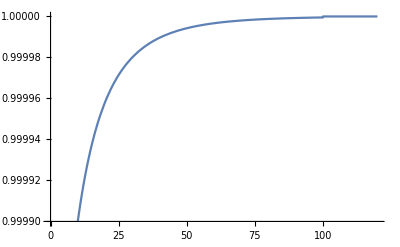

```mathematica
Plot[Fd2[y],{y,0,120}]
```

```mathematica
1->12
```

```mathematica
ξ[x_,y_,z_]:=(y-x+2*x1*√(z+x))/(2*x1*√y);M1[x_,y_,z_,β_]:=((2*π)/(α*β))^2*(√Abs[1-ξ[x,y,z]^2]*√(y*z)*(y-x-(α*β* λ[y,β] x)/(2(1-x-λ[y,β]^2))Exp[(-2y)/β])^2)/(x*√(x+z)((x1-√(x+z))^2-z))*UnitStep[1-ξ[x,y,z]]*UnitStep[y-x];
In1[x_,y_,z_,β_]:=M1[x,y,z,β]*(1+(α*β)/(2*π)*dH[x,y,β])^-1;
```

```mathematica
WW1={};x1=.;
For[x1=0, x1≤ 2.75,WW1=Append[WW1,{x1,NIntegrate[In1[Fd[y],y,z,150],{y,0,∞},{z,0,∞},Method  -> QuasiMonteCarlo, MaxPoints-> 100000,Compiled->False,PrecisionGoal->2]}],x1=x1+0.25]
```

NIntegrate::maxp: The integral failed to converge after 100000 integrand evaluations. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000 integrand evaluations. NIntegrate obtained 7.85951×10^-7 and 5.41717×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

```mathematica
WW1
```

{{0.25,0.},{0.5,0.},{0.75,7.85951×10^-7},{1.,0.00223078},{1.25,0.0426439},{1.5,0.191101},{1.75,0.449887},{2.,0.763929},{2.25,1.11827},{2.5,1.45803},{2.75,1.75632},{3.,2.03146}}

```mathematica
WW2={};x1=.;
For[x1=0, x1≤ 2.75,WW2=Append[WW2,{x1,NIntegrate[In1[Fd2[y],y,z,150],{y,0,∞},{z,0,∞},Method  -> QuasiMonteCarlo, MaxPoints-> 100000,Compiled->False,PrecisionGoal->2]}],x1=x1+0.25]
```

NIntegrate::maxp: The integral failed to converge after 100000 integrand evaluations. NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

```mathematica
WW2
```

{{0.25,0.},{0.5,0.},{0.75,0.},{1.,0.},{1.25,0.00362778},{1.5,0.0247007},{1.75,0.0738256},{2.,0.156058},{2.25,0.271466},{2.5,0.418192},{2.75,0.585331},{3.,0.775779}}

```mathematica
1->22
```

```mathematica
11
```

```mathematica
Dom0[x1_,kx_,ky_]:=(x1^2+Fd[kx^2+ky^2]-Fd[x1^2+kx^2+ky^2-2*x1*kx])^2-4x1^2 Fd[kx^2+ky^2];
M122[x1_,x_,x2_,kx_,ky_,β_]:=(π/(α*β))^2*((x1^2-x-x2)^2)/(x*x1*x2*((x1^2+x-x2)^2-4 x1^2 x)^0.5)*(kx*(x1^2+kx^2+ky^2-2*x1*kx-x2-(α*β*x2*λ[x1^2+kx^2+ky^2-2*x1*kx,β])/(2(1-x2-λ[x1^2+kx^2+ky^2-2*x1*kx,β]^2)))+(x1-kx)(kx^2+ky^2-x-(α*β*x*λ[kx^2+ky^2,β])/(2(1-x-λ[kx^2+ky^2,β]^2))))^2*UnitStep[kx^2+ky^2-x];
```

```mathematica
In11[x1_,kx_,ky_,β_]:=If[Re[Dom0[x1,kx,ky]]≥0,M122[x1,Fd[kx^2+ky^2],Fd[x1^2+kx^2+ky^2-2*x1*kx],kx,ky,β]*(1+(α*β)/(2*π)*dH[Fd[kx^2+ky^2],kx^2+ky^2,β])^-1*(1+(α*β)/(2*π)*dH[Fd[x1^2+kx^2+ky^2-2*x1*kx],x1^2+kx^2+ky^2-2*x1*kx,β])^-1,0];WW11={};x1=.;
For[x1=0.75, x1≤ 2.75,WW11=Append[WW11,{x1,NIntegrate[In11[x1,kx,ky,150],{kx,-∞,∞},{ky,-∞,∞},Method  -> QuasiMonteCarlo, MaxPoints-> 100000,Compiled->False,PrecisionGoal->2]}],x1=x1+0.25]
```

NIntegrate::maxp: The integral failed to converge after 100000 integrand evaluations. NIntegrate obtained -0.0001362 and 0.0000631553 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000 integrand evaluations. NIntegrate obtained -0.196036 and 0.250697 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000 integrand evaluations. NIntegrate obtained 0.0705501 and 0.00587914 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

```mathematica
12
```

```mathematica
Dom1[x1_,kx_,ky_]:=(x1^2+Fd[kx^2+ky^2]-Fd2[x1^2+kx^2+ky^2-2*x1*kx])^2-4x1^2 Fd[kx^2+ky^2];In12[x1_,kx_,ky_,β_]:=If[Re[Dom1[x1,kx,ky]]≥0,M122[x1,Fd[kx^2+ky^2],Fd2[x1^2+kx^2+ky^2-2*x1*kx],kx,ky,β]*(1+(α*β)/(2*π)*dH[Fd[kx^2+ky^2],kx^2+ky^2,β])^-1*(1+(α*β)/(2*π)*dH[Fd2[x1^2+kx^2+ky^2-2*x1*kx],x1^2+kx^2+ky^2-2*x1*kx,β])^-1,0];
WW12={};x1=.;
For[x1=2, x1≤2.08,WW12=Append[WW12,{x1,NIntegrate[In12[x1,kx,ky,150],{kx,-∞,∞},{ky,-∞,∞},Method  -> QuasiMonteCarlo, MaxPoints-> 100000,Compiled->False,PrecisionGoal->2]}],x1=x1+0.01]
```

NIntegrate::maxp: The integral failed to converge after 100000 integrand evaluations. NIntegrate obtained 0.0746535+2.46996×10^-8 ⅈ and 0.00086789 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000 integrand evaluations. NIntegrate obtained 0.0691212+1.82458×10^-8 ⅈ and 0.00084452 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000 integrand evaluations. NIntegrate obtained 0.0659505+1.55628×10^-8 ⅈ and 0.000830486 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

```mathematica
WW12
```

{{2.01,0.0746535},{2.02,0.0691212},{2.03,0.0659505},{2.04,0.0638142},{2.05,0.0622614},{2.06,0.061085},{2.07,0.0601673},{2.08,0.0594397},{2.09,0.0588569}}